```mathematica
FindMaximum[{(81x+19)^1+(80(1-x)+20)^1,0≤x≤1},x]
```

{120.,{x→1.}}

```mathematica
FindMaximum[{(81x+19)^0.5+(80(1-x)+20)^0.5,0≤x≤1},x]
```

{15.4601,{x→0.512327}}

```mathematica
FindMaximum[{Log[81x+19]+Log[80(1-x)+20],0≤x≤1},x]
```

{8.18043,{x→0.507716}}

```mathematica
Welfare[x_,y_,z_]:=Log[81x+19]+Log[80 y+20]+Log[60z+40]
```

```mathematica
FindMaximum[{Welfare[x,y,z],0<x<1, 0<y<1,0<z<1, x+y+z==1},{x,y,z}]
```

{11.8731,{x→0.48251,y→0.467078,z→0.0504124}}

```mathematica
Welfare2[x_,y_] := Welfare[x,y,1-x-y]
```

```mathematica
FindMaximum[{Log[81x+19]+Log[80 y+20]+Log[60(1-x-y)+40],0<x<1, 0<y<1,x+y<1},{x,y}]
```

FindMaximum::nrnum: The function value -11.1219-3.14159 ⅈ is not a real number at {x,y} = {0.9,0.9}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindMaximum::nrnum: The function value -11.1219-3.14159 ⅈ is not a real number at {x,y} = {0.9,0.9}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::eit: The algorithm does not converge to the tolerance of 1.×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {12.009,0.00428498,2.4057}, is returned.

FindMaximum[{Log[81 x+19]+Log[80 y+20]+Log[60 (1-x-y)+40],0<x<1,0<y<1,x+y<1},{x,y}]

```mathematica
FindMaximum[{Welfare2[x,y],0<x<1,0<y<1,0<x+y<1},{{x,0},{y,0}}]
```

{11.8731,{x→0.48251,y→0.467078}}

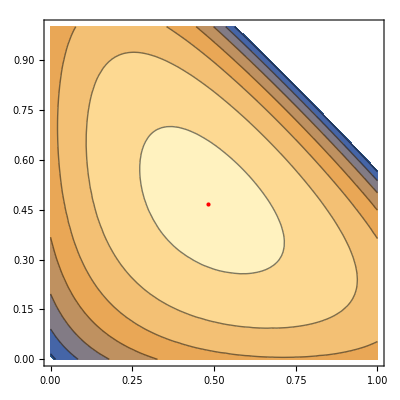

```mathematica
Show[ContourPlot[Welfare2[x,y],{x,0,1},{y,0,1}],Graphics[{Red,PointSize[Large],Point[{x,y}/.Last[%]]}]]
```

```mathematica
{11.873109170468148,{x->0.48250998446251436,y->0.46707789151865764}}
```

{11.8731,{x→0.48251,y→0.467078}}

-Graphics-